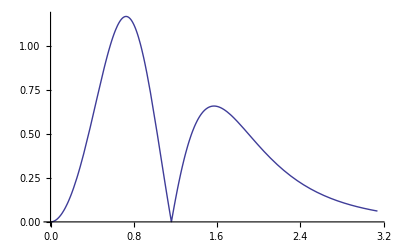

```mathematica
(*Зададим подынтегральную функцию*)
f[x_]=1/(x^2+Cos[x]^2);
(*Зададим отрезок интегрирования*)
a=0;
b=Pi;
(*Зададим точность вычислений*)
eps=10^(-3);
(*Найдем производную второго порядка подынтегральной функции и построим график ее модуля на отрезке интегрирования*)
f2[x_]=D[f[x],{x,2}];
Plot[Abs[f2[x]],{x,a,b}]
```

```mathematica
(*Оценим сверху модуль производной второго порядка подынтегральной функции на отрезке интегрирования*)
M=2;
```

```mathematica
(*Найдем количество частичных отрезков, используя формулу оценки погрешности формулы средних прямоугольников*)
n=Floor[Sqrt[(b-a)^3*M/(24*eps)]]+1;
(*Зададим шаг разбиения*)
h=(b-a)/n;
(*Построим разбиение отрезка интегрирования*)
X=Table[a+k*h,{k,0,n}];
(*Найдем приближенное значение интеграла, используя формулу средних прямоугольников*)
IC=N[h*Sum[f[X[[k]]+h/2],{k,1,n}]];
(*Найдем значение интеграла, используя встроенную функцию численного интегрирования*)
RV=NIntegrate[f[x],{x,a,b}];
Print["Значение интеграла по формуле средних прямоугольников равно: ",IC]
Print["Значение интеграла по встроенной функции равно: ",RV]
Print["Погрешность вычисления равна: ",Abs[IC-RV]]
```

Значение интеграла по формуле средних прямоугольников равно: 1.5812

Значение интеграла по встроенной функции равно: 1.58119

Погрешность вычисления равна: 8.40629×10^-6

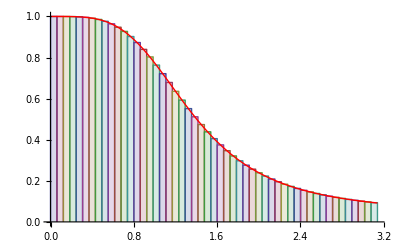

```mathematica
(*Выполним геометрическую иллюстрацию формулы средних прямоугольников*)
(*Зададим средние прямуогольники*)Points=Table[Join[{{X[[k]],0}},{{X[[k]],f[X[[k]]+h/2]}},{{X[[k+1]],f[X[[k]]+h/2]}},{{X[[k+1]],0}}],{k,1,n}];
(*Построим график подынтегральной функции и построенные прямоугольники в одной системе координат*)
GP=ListLinePlot[Points,Filling->Axis];
G=Plot[f[x],{x,a,b},PlotStyle->Red];
Show[GP,G]
```